```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=
β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[2m],Join[Table[{i,i-1},{i,Range[2,2m,1]}],Table[{i,i+1},{i,Range[1,2m,1]}],Table[{2n-1,2m-2n+2},{n,(m+1)/2}],Table[{2m-2n+2,2n-1},{n,(m-1)/2}]]->-t]
```

```mathematica
T1[t_,m_]:=T1[t,m]=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2m-2n+1},{n,(m-1)/2}]->t]
```

```mathematica
ρ[t_,m_]:=ReplacePart[0*IdentityMatrix[2m],Table[{2n,2n},{n,(m-1)/2}]->t]
```

```mathematica
Clear[LEFT,SR]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_,m_]:=LEFT[ω,δ,t,ϵ,m]=Module[{J=Inverse[β[ω,δ,t,ϵ,m]],B:=Inverse[β[ω,δ,t,ϵ,m]],T1:=T1[t,m]},Do[J=Inverse[IdentityMatrix[2m]-B.ConjugateTranspose[T1].J.T1].B,28000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_,m_]:= Inverse[β[ω,δ,t,ϵ,m]]
SR[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]=Inverse[IdentityMatrix[2m]-g[ω,δ,t,ϵ,m].ConjugateTranspose[T1[t,m]].LEFT[ω,δ,t,ϵ,m].T1[t,m]].g[ω,δ,t,ϵ,m]
```

```mathematica
SL[ω_,δ_,t_,ϵ_,m_]:=SR[ω,δ,t,ϵ,m]
```

```mathematica
IL[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SL[ω,δ,t,ϵ,m].ρ[t,m].SR[ω,δ,t,ϵ,m].ρ[t,m]].SL[ω,δ,t,ϵ,m]
```

```mathematica
IR[ω_,δ_,t_,ϵ_,m_]:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,ϵ,m].ρ[t,m].SL[ω,δ,t,ϵ,m].ρ[t,m]].SR[ω,δ,t,ϵ,m]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_,m_]:= IL[ω,δ,t,ϵ,m]-ConjugateTranspose[IL[ω,δ,t,ϵ,m]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_,m_]:= IR[ω,δ,t,ϵ,m]-ConjugateTranspose[IR[ω,δ,t,ϵ,m]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_,m_]:= SR[ω,δ,t,ϵ,m].ρ[t,m].IL[ω,δ,t,ϵ,m]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_,m_]:= Gnonlocal[ω,δ,t,ϵ,m]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ,m]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_,m_]:=Abs[Tr[gdd[ω,δ,t,ϵ,m].ρ[t,m].grr[ω,δ,t,ϵ,m].ρ[t,m]-ρ[t,m].GNON[ω,δ,t,ϵ,m].ρ[t,m].GNON[ω,δ,t,ϵ,m]]]
```

```mathematica
Timing[tr[0.1,0.0001,0.15,0,15]]
```

{74.2474,4.99216}

```mathematica
Table[{ω,tr[ω,0.0001,0.11,0,15]},{ω,Range[-.4,.4,0.001]}]
```

{{-0.4,7.74458×10^-7},{-0.399,7.95033×10^-7},{-0.398,8.1641×10^-7},{-0.397,8.38631×10^-7},{-0.396,8.6174×10^-7},{-0.395,8.85787×10^-7},{-0.394,9.10823×10^-7},{-0.393,9.36902×10^-7},{-0.392,9.64085×10^-7},{-0.391,9.92434×10^-7},{-0.39,1.02202×10^-6},{-0.389,1.05291×10^-6},{-0.388,1.08519×10^-6},{-0.387,1.11894×10^-6},{-0.386,1.15425×10^-6},{-0.385,1.19122×10^-6},{-0.384,1.22997×10^-6},{-0.383,1.27059×10^-6},{-0.382,1.31323×10^-6},{-0.381,1.35801×10^-6},{-0.38,1.40509×10^-6},{-0.379,1.45463×10^-6},{-0.378,1.5068×10^-6},{-0.377,1.56179×10^-6},{-0.376,1.61982×10^-6},{-0.375,1.68111×10^-6},{-0.374,1.74593×10^-6},{-0.373,1.81454×10^-6},{-0.372,1.88726×10^-6},{-0.371,1.96444×10^-6},{-0.37,2.04643×10^-6},{-0.369,2.13368×10^-6},{-0.368,2.22663×10^-6},{-0.367,2.32582×10^-6},{-0.366,2.43181×10^-6},{-0.365,2.54528×10^-6},{-0.364,2.66695×10^-6},{-0.363,2.79764×10^-6},{-0.362,2.93831×10^-6},{-0.361,3.09002×10^-6},{-0.36,3.25397×10^-6},{-0.359,3.43158×10^-6},{-0.358,3.62443×10^-6},{-0.357,3.83439×10^-6},{-0.356,4.06358×10^-6},{-0.355,4.31452×10^-6},{-0.354,4.59013×10^-6},{-0.353,4.89387×10^-6},{-0.352,5.22983×10^-6},{-0.351,5.60288×10^-6},{-0.35,6.01892×10^-6},{-0.349,6.48503×10^-6},{-0.348,7.0099×10^-6},{-0.347,7.60424×10^-6},{-0.346,8.28133×10^-6},{-0.345,9.05793×10^-6},{-0.344,9.95534×10^-6},{-0.343,0.000011001},{-0.342,0.000012231},{-0.341,0.000013693},{-0.34,0.000015452},{-0.339,0.0000175978},{-0.338,0.0000202574},{-0.337,0.0000236164},{-0.336,0.0000279538},{-0.335,0.0000337063},{-0.334,0.0000415889},{-0.333,0.0000528406},{-0.332,0.0000697665},{-0.331,0.0000970683},{-0.33,0.000145611},{-0.329,0.000245465},{-0.328,0.000507657},{-0.327,0.00165106},{-0.326,0.0422948},{-0.325,0.995861},{-0.324,0.999219},{-0.323,0.999696},{-0.322,0.999853},{-0.321,0.999929},{-0.32,0.999978},{-0.319,1.00002},{-0.318,1.00007},{-0.317,1.00014},{-0.316,1.0003},{-0.315,1.00079},{-0.314,1.00439},{-0.313,1.96504},{-0.312,1.99839},{-0.311,1.9995},{-0.31,1.99976},{-0.309,1.99986},{-0.308,1.99991},{-0.307,1.99994},{-0.306,1.99996},{-0.305,1.99997},{-0.304,1.99998},{-0.303,1.99999},{-0.302,2.},{-0.301,2.00002},{-0.3,2.00003},{-0.299,2.00005},{-0.298,2.00008},{-0.297,2.00013},{-0.296,2.00025},{-0.295,2.00056},{-0.294,2.00212},{-0.293,2.19559},{-0.292,2.99707},{-0.291,2.99931},{-0.29,2.9997},{-0.289,2.99983},{-0.288,2.99989},{-0.287,2.99992},{-0.286,2.99995},{-0.285,2.99996},{-0.284,2.99997},{-0.283,2.99998},{-0.282,2.99998},{-0.281,2.99999},{-0.28,2.99999},{-0.279,3.},{-0.278,3.},{-0.277,3.},{-0.276,3.00001},{-0.275,3.00002},{-0.274,3.00002},{-0.273,3.00003},{-0.272,3.00005},{-0.271,3.00007},{-0.27,3.00012},{-0.269,3.0002},{-0.268,3.00041},{-0.267,3.00119},{-0.266,3.01259},{-0.265,3.99228},{-0.264,3.99897},{-0.263,3.99961},{-0.262,3.9998},{-0.261,3.99987},{-0.26,3.99991},{-0.259,3.99994},{-0.258,3.99995},{-0.257,3.99996},{-0.256,3.99997},{-0.255,3.99998},{-0.254,3.99998},{-0.253,3.99998},{-0.252,3.99999},{-0.251,3.99999},{-0.25,3.99999},{-0.249,4.},{-0.248,4.},{-0.247,4.},{-0.246,4.},{-0.245,4.00001},{-0.244,4.00001},{-0.243,4.00001},{-0.242,4.00002},{-0.241,4.00002},{-0.24,4.00003},{-0.239,4.00005},{-0.238,4.00007},{-0.237,4.0001},{-0.236,4.00017},{-0.235,4.00032},{-0.234,4.00078},{-0.233,4.0041},{-0.232,4.957},{-0.231,4.99833},{-0.23,4.99949},{-0.229,4.99975},{-0.228,4.99985},{-0.227,4.9999},{-0.226,4.99993},{-0.225,4.99995},{-0.224,4.99996},{-0.223,4.99997},{-0.222,4.99997},{-0.221,4.99998},{-0.22,4.99998},{-0.219,4.99999},{-0.218,4.99999},{-0.217,4.99999},{-0.216,4.99999},{-0.215,4.99999},{-0.214,4.99999},{-0.213,5.},{-0.212,5.},{-0.211,5.},{-0.21,5.},{-0.209,5.},{-0.208,5.00001},{-0.207,5.00001},{-0.206,5.00001},{-0.205,5.00001},{-0.204,5.00002},{-0.203,5.00003},{-0.202,5.00003},{-0.201,5.00005},{-0.2,5.00007},{-0.199,5.0001},{-0.198,5.00017},{-0.197,5.00031},{-0.196,5.00075},{-0.195,5.00376},{-0.194,5.94261},{-0.193,5.99824},{-0.192,5.99947},{-0.191,5.99975},{-0.19,5.99985},{-0.189,5.9999},{-0.188,5.99993},{-0.187,5.99995},{-0.186,5.99996},{-0.185,5.99997},{-0.184,5.99997},{-0.183,5.99998},{-0.182,5.99998},{-0.181,5.99998},{-0.18,5.99999},{-0.179,5.99999},{-0.178,5.99999},{-0.177,5.99999},{-0.176,5.99999},{-0.175,5.99999},{-0.174,6.},{-0.173,6.},{-0.172,6.},{-0.171,6.},{-0.17,6.},{-0.169,6.},{-0.168,6.},{-0.167,6.00001},{-0.166,6.00001},{-0.165,6.00001},{-0.164,6.00001},{-0.163,6.00002},{-0.162,6.00003},{-0.161,6.00003},{-0.16,6.00005},{-0.159,6.00006},{-0.158,6.00009},{-0.157,6.00015},{-0.156,6.00026},{-0.155,6.00058},{-0.154,6.00214},{-0.153,6.18749},{-0.152,6.99709},{-0.151,6.99933},{-0.15,6.99971},{-0.149,6.99984},{-0.148,6.99989},{-0.147,6.99993},{-0.146,6.99994},{-0.145,6.99996},{-0.144,6.99996},{-0.143,6.99997},{-0.142,6.99997},{-0.141,6.99998},{-0.14,6.99998},{-0.139,6.99998},{-0.138,6.99998},{-0.137,6.99998},{-0.136,6.99998},{-0.135,6.99999},{-0.134,6.99999},{-0.133,6.99999},{-0.132,6.99999},{-0.131,6.99999},{-0.13,6.99999},{-0.129,6.99999},{-0.128,6.99999},{-0.127,6.99999},{-0.126,6.99999},{-0.125,6.99998},{-0.124,6.99998},{-0.123,6.99998},{-0.122,6.99998},{-0.121,6.99998},{-0.12,6.99998},{-0.119,6.99998},{-0.118,6.99997},{-0.117,6.99997},{-0.116,6.99997},{-0.115,6.99996},{-0.114,6.99995},{-0.113,6.99994},{-0.112,6.99992},{-0.111,6.99989},{-0.11,6.99984},{-0.109,6.99974},{-0.108,6.99948},{-0.107,6.99832},{-0.106,6.95758},{-0.105,6.0041},{-0.104,6.00076},{-0.103,6.00029},{-0.102,6.00013},{-0.101,6.00006},{-0.1,6.00001},{-0.099,5.99997},{-0.098,5.99992},{-0.097,5.99984},{-0.096,5.99968},{-0.095,5.99919},{-0.094,5.99557},{-0.093,5.03486},{-0.092,5.00158},{-0.091,5.00049},{-0.09,5.00023},{-0.089,5.00013},{-0.088,5.00008},{-0.087,5.00005},{-0.086,5.00003},{-0.085,5.00002},{-0.084,5.00001},{-0.083,5.},{-0.082,4.99999},{-0.081,4.99997},{-0.08,4.99996},{-0.079,4.99994},{-0.078,4.9999},{-0.077,4.99984},{-0.076,4.99972},{-0.075,4.9994},{-0.074,4.99782},{-0.073,4.8042},{-0.072,4.00283},{-0.071,4.00054},{-0.07,4.00004},{-0.069,3.99955},{-0.068,3.9973},{-0.067,3.18834},{-0.066,3.00229},{-0.065,3.00067},{-0.064,3.00033},{-0.063,3.0002},{-0.062,3.00014},{-0.061,3.0001},{-0.06,3.00007},{-0.059,3.00006},{-0.058,3.00004},{-0.057,3.00003},{-0.056,3.00002},{-0.055,3.00001},{-0.054,3.},{-0.053,2.99999},{-0.052,2.99997},{-0.051,2.99994},{-0.05,2.9999},{-0.049,2.99981},{-0.048,2.9996},{-0.047,2.99882},{-0.046,2.98742},{-0.045,2.00774},{-0.044,2.00104},{-0.043,2.0004},{-0.042,2.00021},{-0.041,2.00013},{-0.04,2.00009},{-0.039,2.00007},{-0.038,2.00005},{-0.037,2.00004},{-0.036,2.00003},{-0.035,2.00002},{-0.034,2.00001},{-0.033,1.99999},{-0.032,1.99998},{-0.031,1.99995},{-0.03,1.99991},{-0.029,1.99981},{-0.028,1.99956},{-0.027,1.99838},{-0.026,1.94334},{-0.025,1.00396},{-0.024,1.00085},{-0.023,1.00038},{-0.022,1.00021},{-0.021,1.00014},{-0.02,1.00009},{-0.019,1.00005},{-0.018,1.00002},{-0.017,0.999982},{-0.016,0.999916},{-0.015,0.999776},{-0.014,0.999336},{-0.013,0.996124},{-0.012,0.0436484},{-0.011,0.00183774},{-0.01,0.000625295},{-0.009,0.000338205},{-0.008,0.000225827},{-0.007,0.000170074},{-0.006,0.000138413},{-0.005,0.000118912},{-0.004,0.000106353},{-0.003,0.0000981718},{-0.002,0.0000930184},{-0.001,0.0000901659},{0.,0.0000892518},{0.001,0.0000901659},{0.002,0.0000930184},{0.003,0.0000981718},{0.004,0.000106353},{0.005,0.000118912},{0.006,0.000138413},{0.007,0.000170074},{0.008,0.000225827},{0.009,0.000338205},{0.01,0.000625295},{0.011,0.00183774},{0.012,0.0436484},{0.013,0.996124},{0.014,0.999336},{0.015,0.999776},{0.016,0.999916},{0.017,0.999982},{0.018,1.00002},{0.019,1.00005},{0.02,1.00009},{0.021,1.00014},{0.022,1.00021},{0.023,1.00038},{0.024,1.00085},{0.025,1.00396},{0.026,1.94334},{0.027,1.99838},{0.028,1.99956},{0.029,1.99981},{0.03,1.99991},{0.031,1.99995},{0.032,1.99998},{0.033,1.99999},{0.034,2.00001},{0.035,2.00002},{0.036,2.00003},{0.037,2.00004},{0.038,2.00005},{0.039,2.00007},{0.04,2.00009},{0.041,2.00013},{0.042,2.00021},{0.043,2.0004},{0.044,2.00104},{0.045,2.00774},{0.046,2.98742},{0.047,2.99882},{0.048,2.9996},{0.049,2.99981},{0.05,2.9999},{0.051,2.99994},{0.052,2.99997},{0.053,2.99999},{0.054,3.},{0.055,3.00001},{0.056,3.00002},{0.057,3.00003},{0.058,3.00004},{0.059,3.00006},{0.06,3.00007},{0.061,3.0001},{0.062,3.00014},{0.063,3.0002},{0.064,3.00033},{0.065,3.00067},{0.066,3.00229},{0.067,3.18834},{0.068,3.9973},{0.069,3.99955},{0.07,4.00004},{0.071,4.00054},{0.072,4.00283},{0.073,4.8042},{0.074,4.99782},{0.075,4.9994},{0.076,4.99972},{0.077,4.99984},{0.078,4.9999},{0.079,4.99994},{0.08,4.99996},{0.081,4.99997},{0.082,4.99999},{0.083,5.},{0.084,5.00001},{0.085,5.00002},{0.086,5.00003},{0.087,5.00005},{0.088,5.00008},{0.089,5.00013},{0.09,5.00023},{0.091,5.00049},{0.092,5.00158},{0.093,5.03486},{0.094,5.99557},{0.095,5.99919},{0.096,5.99968},{0.097,5.99984},{0.098,5.99992},{0.099,5.99997},{0.1,6.00001},{0.101,6.00006},{0.102,6.00013},{0.103,6.00029},{0.104,6.00076},{0.105,6.0041},{0.106,6.95758},{0.107,6.99832},{0.108,6.99948},{0.109,6.99974},{0.11,6.99984},{0.111,6.99989},{0.112,6.99992},{0.113,6.99994},{0.114,6.99995},{0.115,6.99996},{0.116,6.99997},{0.117,6.99997},{0.118,6.99997},{0.119,6.99998},{0.12,6.99998},{0.121,6.99998},{0.122,6.99998},{0.123,6.99998},{0.124,6.99998},{0.125,6.99998},{0.126,6.99999},{0.127,6.99999},{0.128,6.99999},{0.129,6.99999},{0.13,6.99999},{0.131,6.99999},{0.132,6.99999},{0.133,6.99999},{0.134,6.99999},{0.135,6.99999},{0.136,6.99998},{0.137,6.99998},{0.138,6.99998},{0.139,6.99998},{0.14,6.99998},{0.141,6.99998},{0.142,6.99997},{0.143,6.99997},{0.144,6.99996},{0.145,6.99996},{0.146,6.99994},{0.147,6.99993},{0.148,6.99989},{0.149,6.99984},{0.15,6.99971},{0.151,6.99933},{0.152,6.99709},{0.153,6.18749},{0.154,6.00214},{0.155,6.00058},{0.156,6.00026},{0.157,6.00015},{0.158,6.00009},{0.159,6.00006},{0.16,6.00005},{0.161,6.00003},{0.162,6.00003},{0.163,6.00002},{0.164,6.00001},{0.165,6.00001},{0.166,6.00001},{0.167,6.00001},{0.168,6.},{0.169,6.},{0.17,6.},{0.171,6.},{0.172,6.},{0.173,6.},{0.174,6.},{0.175,5.99999},{0.176,5.99999},{0.177,5.99999},{0.178,5.99999},{0.179,5.99999},{0.18,5.99999},{0.181,5.99998},{0.182,5.99998},{0.183,5.99998},{0.184,5.99997},{0.185,5.99997},{0.186,5.99996},{0.187,5.99995},{0.188,5.99993},{0.189,5.9999},{0.19,5.99985},{0.191,5.99975},{0.192,5.99947},{0.193,5.99824},{0.194,5.94261},{0.195,5.00376},{0.196,5.00075},{0.197,5.00031},{0.198,5.00017},{0.199,5.0001},{0.2,5.00007},{0.201,5.00005},{0.202,5.00003},{0.203,5.00003},{0.204,5.00002},{0.205,5.00001},{0.206,5.00001},{0.207,5.00001},{0.208,5.00001},{0.209,5.},{0.21,5.},{0.211,5.},{0.212,5.},{0.213,5.},{0.214,4.99999},{0.215,4.99999},{0.216,4.99999},{0.217,4.99999},{0.218,4.99999},{0.219,4.99999},{0.22,4.99998},{0.221,4.99998},{0.222,4.99997},{0.223,4.99997},{0.224,4.99996},{0.225,4.99995},{0.226,4.99993},{0.227,4.9999},{0.228,4.99985},{0.229,4.99975},{0.23,4.99949},{0.231,4.99833},{0.232,4.957},{0.233,4.0041},{0.234,4.00078},{0.235,4.00032},{0.236,4.00017},{0.237,4.0001},{0.238,4.00007},{0.239,4.00005},{0.24,4.00003},{0.241,4.00002},{0.242,4.00002},{0.243,4.00001},{0.244,4.00001},{0.245,4.00001},{0.246,4.},{0.247,4.},{0.248,4.},{0.249,4.},{0.25,3.99999},{0.251,3.99999},{0.252,3.99999},{0.253,3.99998},{0.254,3.99998},{0.255,3.99998},{0.256,3.99997},{0.257,3.99996},{0.258,3.99995},{0.259,3.99994},{0.26,3.99991},{0.261,3.99987},{0.262,3.9998},{0.263,3.99961},{0.264,3.99897},{0.265,3.99228},{0.266,3.01259},{0.267,3.00119},{0.268,3.00041},{0.269,3.0002},{0.27,3.00012},{0.271,3.00007},{0.272,3.00005},{0.273,3.00003},{0.274,3.00002},{0.275,3.00002},{0.276,3.00001},{0.277,3.},{0.278,3.},{0.279,3.},{0.28,2.99999},{0.281,2.99999},{0.282,2.99998},{0.283,2.99998},{0.284,2.99997},{0.285,2.99996},{0.286,2.99995},{0.287,2.99992},{0.288,2.99989},{0.289,2.99983},{0.29,2.9997},{0.291,2.99931},{0.292,2.99707},{0.293,2.19559},{0.294,2.00212},{0.295,2.00056},{0.296,2.00025},{0.297,2.00013},{0.298,2.00008},{0.299,2.00005},{0.3,2.00003},{0.301,2.00002},{0.302,2.},{0.303,1.99999},{0.304,1.99998},{0.305,1.99997},{0.306,1.99996},{0.307,1.99994},{0.308,1.99991},{0.309,1.99986},{0.31,1.99976},{0.311,1.9995},{0.312,1.99839},{0.313,1.96504},{0.314,1.00439},{0.315,1.00079},{0.316,1.0003},{0.317,1.00014},{0.318,1.00007},{0.319,1.00002},{0.32,0.999978},{0.321,0.999929},{0.322,0.999853},{0.323,0.999696},{0.324,0.999219},{0.325,0.995861},{0.326,0.0422948},{0.327,0.00165106},{0.328,0.000507657},{0.329,0.000245465},{0.33,0.000145611},{0.331,0.0000970683},{0.332,0.0000697665},{0.333,0.0000528406},{0.334,0.0000415889},{0.335,0.0000337063},{0.336,0.0000279538},{0.337,0.0000236164},{0.338,0.0000202574},{0.339,0.0000175978},{0.34,0.000015452},{0.341,0.000013693},{0.342,0.000012231},{0.343,0.000011001},{0.344,9.95534×10^-6},{0.345,9.05793×10^-6},{0.346,8.28133×10^-6},{0.347,7.60424×10^-6},{0.348,7.0099×10^-6},{0.349,6.48503×10^-6},{0.35,6.01892×10^-6},{0.351,5.60288×10^-6},{0.352,5.22983×10^-6},{0.353,4.89387×10^-6},{0.354,4.59013×10^-6},{0.355,4.31452×10^-6},{0.356,4.06358×10^-6},{0.357,3.83439×10^-6},{0.358,3.62443×10^-6},{0.359,3.43158×10^-6},{0.36,3.25397×10^-6},{0.361,3.09002×10^-6},{0.362,2.93831×10^-6},{0.363,2.79764×10^-6},{0.364,2.66695×10^-6},{0.365,2.54528×10^-6},{0.366,2.43181×10^-6},{0.367,2.32582×10^-6},{0.368,2.22663×10^-6},{0.369,2.13368×10^-6},{0.37,2.04643×10^-6},{0.371,1.96444×10^-6},{0.372,1.88726×10^-6},{0.373,1.81454×10^-6},{0.374,1.74593×10^-6},{0.375,1.68111×10^-6},{0.376,1.61982×10^-6},{0.377,1.56179×10^-6},{0.378,1.5068×10^-6},{0.379,1.45463×10^-6},{0.38,1.40509×10^-6},{0.381,1.35801×10^-6},{0.382,1.31323×10^-6},{0.383,1.27059×10^-6},{0.384,1.22997×10^-6},{0.385,1.19122×10^-6},{0.386,1.15425×10^-6},{0.387,1.11894×10^-6},{0.388,1.08519×10^-6},{0.389,1.05291×10^-6},{0.39,1.02202×10^-6},{0.391,9.92434×10^-7},{0.392,9.64085×10^-7},{0.393,9.36902×10^-7},{0.394,9.10823×10^-7},{0.395,8.85787×10^-7},{0.396,8.6174×10^-7},{0.397,8.38631×10^-7},{0.398,8.1641×10^-7},{0.399,7.95033×10^-7},{0.4,7.74458×10^-7}}

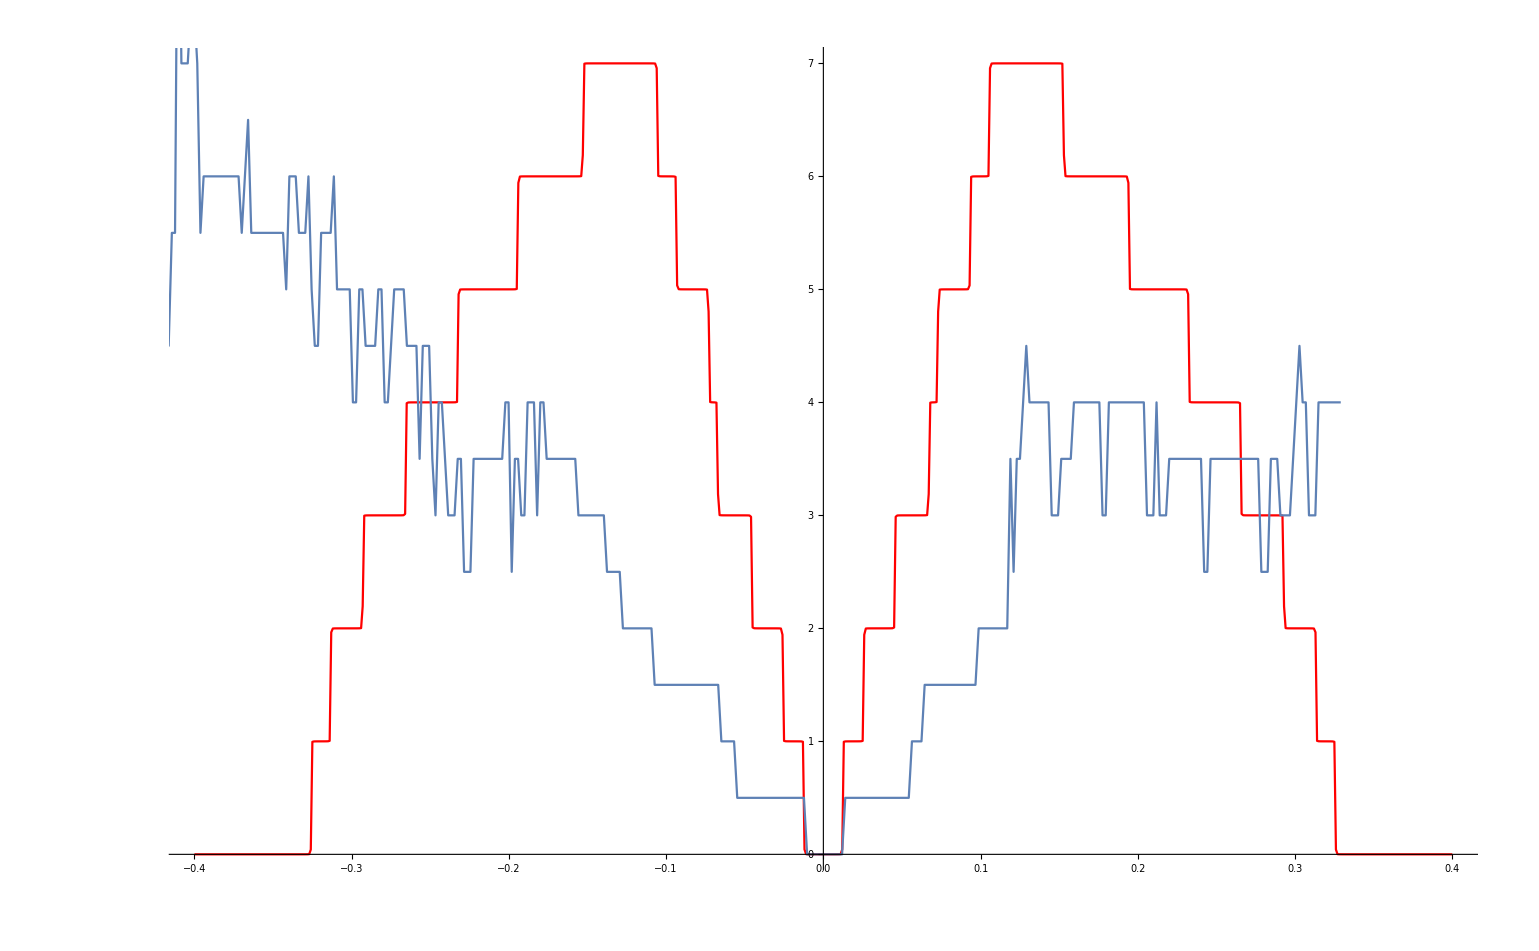

```mathematica
Show[ListPlot[%49,Joined->True,PlotStyle->Red],%47]
```

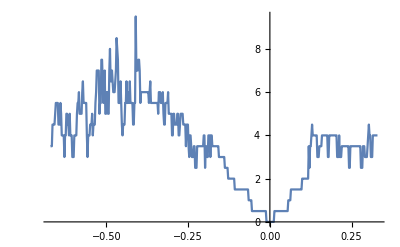

-Graphics-

```mathematica
data:=data=Import["/home/shardulmukim/PhD/fwi/DFT/15AGNR/Impureza.dat"]
```

```mathematica
Table[{data[[x]][[1]]+0.33,data[[x]][[2]]},{x,496}]
```

{{-0.67,5.88714},{-0.66798,5.86028},{-0.66596,5.69189},{-0.663939,7.63503},{-0.661919,7.81437},{-0.659899,7.85808},{-0.657879,7.81396},{-0.655859,7.99111},{-0.653838,8.91246},{-0.651818,9.1066},{-0.649798,9.15361},{-0.647778,9.05387},{-0.645758,7.13166},{-0.643737,7.06554},{-0.641717,7.17113},{-0.639697,8.89077},{-0.637677,8.41467},{-0.635657,6.82035},{-0.633636,6.6025},{-0.631616,6.55336},{-0.629596,6.2095},{-0.627576,5.21998},{-0.625556,6.82002},{-0.623535,6.92841},{-0.621515,8.23431},{-0.619495,8.28166},{-0.617475,7.62766},{-0.615455,7.55615},{-0.613434,7.26566},{-0.611414,8.02061},{-0.609394,6.67496},{-0.607374,6.53896},{-0.605354,6.15082},{-0.603333,4.96908},{-0.601313,4.88397},{-0.599293,4.73716},{-0.597273,6.39784},{-0.595253,6.67168},{-0.593232,6.64418},{-0.591212,6.49199},{-0.589192,8.34577},{-0.587172,8.90091},{-0.585152,8.81149},{-0.583131,9.52814},{-0.581111,8.07492},{-0.579091,7.87774},{-0.577071,8.10678},{-0.575051,8.21125},{-0.57303,10.2975},{-0.57101,10.674},{-0.56899,9.67054},{-0.56697,9.65025},{-0.564949,9.6206},{-0.562929,9.5637},{-0.560909,9.38431},{-0.558889,6.48673},{-0.556869,5.36438},{-0.554848,7.13849},{-0.552828,7.1704},{-0.550808,7.15365},{-0.548788,8.00432},{-0.546768,8.01919},{-0.544747,7.77901},{-0.542727,7.35518},{-0.540707,6.96157},{-0.538687,7.00021},{-0.536667,6.99393},{-0.534646,6.75553},{-0.532626,8.20637},{-0.530606,9.06066},{-0.528586,11.3041},{-0.526566,11.6658},{-0.524545,11.8137},{-0.522525,11.6188},{-0.520505,8.3141},{-0.518485,8.4729},{-0.516465,8.83798},{-0.514444,11.538},{-0.512424,12.4544},{-0.510404,10.5203},{-0.508384,9.23878},{-0.506364,9.90459},{-0.504343,11.3157},{-0.502323,8.63881},{-0.500303,8.61943},{-0.498283,10.4553},{-0.496263,10.3507},{-0.494242,8.81067},{-0.492222,8.77149},{-0.490202,10.4028},{-0.488182,12.0234},{-0.486162,11.2532},{-0.484141,11.2375},{-0.482121,11.0705},{-0.480101,11.6131},{-0.478081,9.99545},{-0.476061,10.3906},{-0.47404,9.69937},{-0.47202,10.6454},{-0.47,11.7858},{-0.46798,13.2977},{-0.46596,13.3851},{-0.463939,12.4759},{-0.461919,9.39041},{-0.459899,9.27414},{-0.457879,9.40015},{-0.455859,10.8698},{-0.453838,9.42706},{-0.451818,7.9483},{-0.449798,6.30548},{-0.447778,7.08941},{-0.445758,7.29809},{-0.443737,7.54699},{-0.441717,9.49025},{-0.439697,9.68735},{-0.437677,11.1518},{-0.435657,9.75402},{-0.433636,8.83717},{-0.431616,11.1832},{-0.429596,8.18098},{-0.427576,10.3654},{-0.425556,9.36341},{-0.423535,9.35478},{-0.421515,9.30048},{-0.419495,9.25266},{-0.417475,9.24633},{-0.415455,8.33849},{-0.413434,9.55654},{-0.411414,9.54381},{-0.409394,8.26626},{-0.407374,11.8715},{-0.405354,12.0793},{-0.403333,12.3786},{-0.401313,12.7216},{-0.399293,12.4468},{-0.397273,11.0291},{-0.395253,9.61483},{-0.393232,10.776},{-0.391212,10.8425},{-0.389192,11.2014},{-0.387172,11.2241},{-0.385152,11.1275},{-0.383131,11.0502},{-0.381111,10.9756},{-0.379091,10.8884},{-0.377071,9.83623},{-0.375051,10.8363},{-0.37303,10.4754},{-0.37101,9.8817},{-0.36899,9.63944},{-0.36697,9.64475},{-0.364949,10.542},{-0.362929,8.94507},{-0.360909,8.77387},{-0.358889,10.0146},{-0.356869,9.80208},{-0.354848,9.62112},{-0.352828,9.64249},{-0.350808,9.89571},{-0.348788,10.0107},{-0.346768,10.1446},{-0.344747,10.38},{-0.342727,10.6187},{-0.340707,7.52359},{-0.338687,12.8072},{-0.336667,10.3682},{-0.334646,10.2988},{-0.332626,9.77725},{-0.330606,9.78805},{-0.328586,9.73096},{-0.326566,10.5567},{-0.324545,8.72465},{-0.322525,8.43051},{-0.320505,8.02883},{-0.318485,10.4589},{-0.316465,9.58822},{-0.314444,9.34053},{-0.312424,8.98999},{-0.310404,8.80966},{-0.308384,9.2549},{-0.306364,9.18284},{-0.304343,9.08327},{-0.302323,9.00785},{-0.300303,8.8753},{-0.298283,7.23795},{-0.296263,6.89955},{-0.294242,8.80264},{-0.292222,8.76744},{-0.290202,8.31742},{-0.288182,7.75076},{-0.286162,7.66257},{-0.284141,7.60427},{-0.282121,8.43011},{-0.280101,8.22591},{-0.278081,7.13639},{-0.276061,6.9853},{-0.27404,6.56154},{-0.27202,8.54734},{-0.27,8.80866},{-0.26798,10.4051},{-0.26596,8.36345},{-0.263939,8.25898},{-0.261919,8.15243},{-0.259899,8.05744},{-0.257879,7.94453},{-0.255859,5.92891},{-0.253838,7.84267},{-0.251818,7.81101},{-0.249798,7.77532},{-0.247778,6.7801},{-0.245758,5.47883},{-0.243737,5.97556},{-0.241717,5.25326},{-0.239697,5.77605},{-0.237677,5.42121},{-0.235657,5.19702},{-0.233636,5.05943},{-0.231616,5.99906},{-0.229596,5.69052},{-0.227576,4.88661},{-0.225556,4.72622},{-0.223535,3.99845},{-0.221515,5.86729},{-0.219495,5.94135},{-0.217475,5.96743},{-0.215455,6.00666},{-0.213434,6.07819},{-0.211414,6.1961},{-0.209394,6.36399},{-0.207374,6.56047},{-0.205354,6.73889},{-0.203333,6.8331},{-0.201313,6.75244},{-0.199293,6.54377},{-0.197273,4.93666},{-0.195253,6.22258},{-0.193232,5.82422},{-0.191212,5.61627},{-0.189192,4.89704},{-0.187172,6.78468},{-0.185152,6.76607},{-0.183131,6.37869},{-0.181111,5.81321},{-0.179091,5.69447},{-0.177071,6.60358},{-0.175051,5.53491},{-0.17303,6.72872},{-0.17101,6.74823},{-0.16899,6.72919},{-0.16697,6.7035},{-0.164949,6.67355},{-0.162929,6.63682},{-0.160909,6.58361},{-0.158889,6.47253},{-0.156869,5.58849},{-0.154848,5.6407},{-0.152828,5.52009},{-0.150808,5.42455},{-0.148788,5.33819},{-0.146768,5.25994},{-0.144747,5.18926},{-0.142727,5.12201},{-0.140707,5.04363},{-0.138687,4.89505},{-0.136667,4.08874},{-0.134646,4.00713},{-0.132626,3.94416},{-0.130606,3.90384},{-0.128586,3.86661},{-0.126566,3.91334},{-0.124545,3.85166},{-0.122525,3.82964},{-0.120505,3.81277},{-0.118485,3.79757},{-0.116465,3.78276},{-0.114444,3.76721},{-0.112424,3.74669},{-0.110404,3.71469},{-0.108384,3.63909},{-0.106364,2.81346},{-0.104343,2.9788},{-0.102323,2.95923},{-0.100303,2.94318},{-0.0982828,2.92843},{-0.0962626,2.91373},{-0.0942424,2.89838},{-0.0922222,2.88184},{-0.090202,2.86373},{-0.0881818,2.84378},{-0.0861616,2.8217},{-0.0841414,2.79737},{-0.0821212,2.77136},{-0.080101,2.7423},{-0.0780808,2.70994},{-0.0760606,2.67814},{-0.0740404,2.66269},{-0.0720202,2.60875},{-0.07,2.56136},{-0.0679798,2.64885},{-0.0659596,2.37614},{-0.0639394,1.67486},{-0.0619192,1.66086},{-0.059899,1.6426},{-0.0578788,1.63478},{-0.0558586,1.53116},{-0.0538384,0.979299},{-0.0518182,0.983331},{-0.049798,0.982711},{-0.0477778,0.981124},{-0.0457576,0.979191},{-0.0437374,0.977051},{-0.0417172,0.974629},{-0.039697,0.972025},{-0.0376768,0.969747},{-0.0356566,0.966849},{-0.0336364,0.962706},{-0.0316162,0.958682},{-0.029596,0.95408},{-0.0275758,0.948683},{-0.0255556,0.942062},{-0.0235354,0.933629},{-0.0215151,0.929666},{-0.019495,0.906335},{-0.0174747,0.882185},{-0.0154546,0.839953},{-0.0134343,0.743578},{-0.0114141,0.264998},{-0.00939394,2.88752×10^-19},{-0.00737374,0.},{-0.00535354,7.04788×10^-11},{-0.00333333,4.54319×10^-20},{-0.00131313,0.},{0.00070707,4.07499×10^-19},{0.00272727,0.},{0.00474747,1.7829×10^-19},{0.00676768,0.},{0.00878788,0.},{0.0108081,0.},{0.0128283,1.61389×10^-18},{0.0148485,0.0784724},{0.0168687,0.0331348},{0.0188889,1.52717×10^-6},{0.0209091,0.0449171},{0.0229293,0.15648},{0.0249495,0.30807},{0.0269697,0.397418},{0.0289899,0.545916},{0.0310101,0.632331},{0.0330303,0.671281},{0.0350505,0.709109},{0.0370707,0.771983},{0.0390909,0.849957},{0.0411111,0.819514},{0.0431313,0.835897},{0.0451515,0.848522},{0.0471717,0.858067},{0.0491919,0.864749},{0.0512121,0.868292},{0.0532323,0.874475},{0.0552525,0.904377},{0.0572727,0.889342},{0.0592929,0.616363},{0.0613131,0.250076},{0.0633333,1.02287},{0.0653535,1.59026},{0.0673737,1.83803},{0.0693939,1.928},{0.0714141,1.98865},{0.0734343,2.03681},{0.0754546,2.07831},{0.0774748,2.11536},{0.079495,2.14968},{0.0815152,2.1822},{0.0835354,2.21384},{0.0855556,2.24485},{0.0875758,2.27573},{0.089596,2.30634},{0.0916162,2.33536},{0.0936364,2.41219},{0.0956566,2.37339},{0.0976768,2.33452},{0.099697,3.04879},{0.101717,3.32753},{0.103737,3.4164},{0.105758,3.46981},{0.107778,3.50598},{0.109798,3.52822},{0.111818,3.53428},{0.113838,3.51256},{0.115859,3.42257},{0.117879,2.93085},{0.119899,4.18042},{0.121919,3.98795},{0.123939,5.03522},{0.12596,5.4921},{0.12798,5.69758},{0.13,6.21404},{0.13202,6.36908},{0.13404,6.64928},{0.136061,6.84819},{0.138081,7.09886},{0.140101,7.22089},{0.142121,7.45906},{0.144141,7.46507},{0.146162,6.02179},{0.148182,5.5522},{0.150202,4.98698},{0.152222,6.00057},{0.154242,6.1201},{0.156263,6.0658},{0.158283,5.93756},{0.160303,7.04805},{0.162323,7.1889},{0.164343,7.22505},{0.166364,7.24547},{0.168384,7.26035},{0.170404,7.27403},{0.172424,7.28712},{0.174444,7.29999},{0.176465,7.27898},{0.178485,5.56067},{0.180505,5.27266},{0.182525,7.22835},{0.184545,7.26878},{0.186566,7.27973},{0.188586,7.27785},{0.190606,7.26816},{0.192626,7.22441},{0.194646,7.21483},{0.196667,7.19273},{0.198687,7.1611},{0.200707,7.12351},{0.202727,7.0742},{0.204747,6.87691},{0.206768,5.05599},{0.208788,4.97921},{0.210808,5.11414},{0.212828,6.74584},{0.214848,5.97122},{0.216869,5.83219},{0.218889,5.9099},{0.220909,6.50761},{0.222929,6.6266},{0.224949,6.63827},{0.22697,6.63887},{0.22899,6.63382},{0.23101,6.62627},{0.23303,6.61724},{0.235051,6.60794},{0.237071,6.59778},{0.239091,6.58617},{0.241111,6.56129},{0.243131,4.87573},{0.245152,4.62633},{0.247172,6.13375},{0.249192,6.41452},{0.251212,6.43318},{0.253232,6.42189},{0.255253,6.36163},{0.257273,6.30021},{0.259293,6.21867},{0.261313,6.01379},{0.263333,6.02613},{0.265354,6.48674},{0.267374,6.5811},{0.269394,6.57647},{0.271414,6.549},{0.273434,6.51753},{0.275455,6.47444},{0.277475,6.27911},{0.279495,4.46628},{0.281515,4.28964},{0.283535,4.01837},{0.285556,6.22246},{0.287576,6.24733},{0.289596,6.21344},{0.291616,5.20646},{0.293636,5.90452},{0.295657,5.10728},{0.297677,4.96029},{0.299697,1.98118},{0.301717,6.02311},{0.303737,6.36322},{0.305758,6.73382},{0.307778,5.98787},{0.309798,11.6875},{0.311818,5.30042},{0.313838,5.23425},{0.315859,7.17037},{0.317879,7.21448},{0.319899,7.20514},{0.321919,7.17895},{0.323939,7.15726},{0.32596,7.13775},{0.32798,7.11801},{0.33,7.10087}}

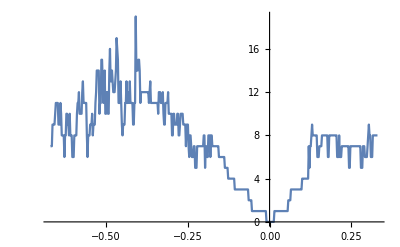

```mathematica
ListPlot[Table[{data[[x]][[1]]+0.33,data[[x]][[6]]},{x,496}],Joined->True]
```

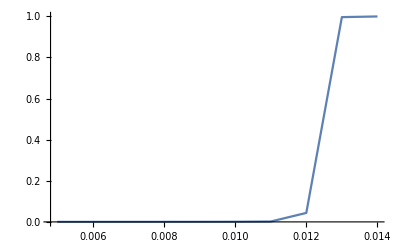

```mathematica
ListPlot[%35,Joined->True]
```

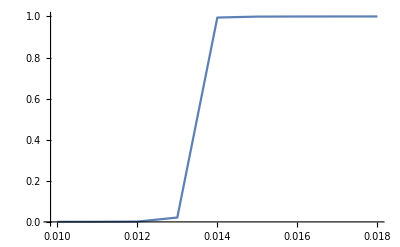

```mathematica
ListPlot[%32,Joined->True]
```

```mathematica
Join[Table[{-ω,tr[ω,0.0001,0.12,0,15]},{ω,Range[0.01,0.018,0.001]}],Table[{ω,tr[ω,0.0001,0.12,0,15]},{ω,Range[0.01,0.018,0.001]}]]
```

$Aborted

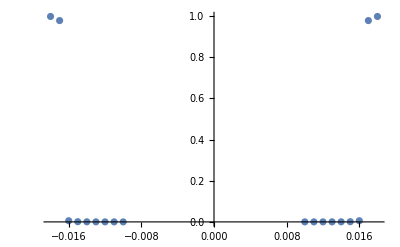

```mathematica
ListPlot[%27]
```

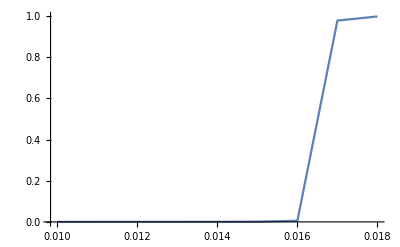

```mathematica
ListPlot[%25,Joined->True]
```

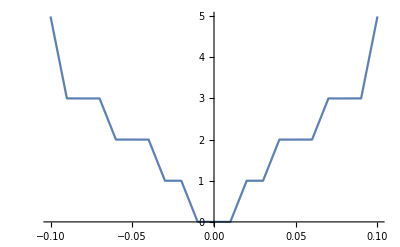

```mathematica
ListPlot[%22,Joined->True]
```